A(τ) as a Gamma(2, 1/2) distribution (noting Mathematica uses scale instead of rate):

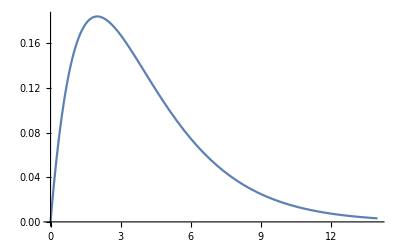

```mathematica
Plot[PDF[GammaDistribution[2,2],x],{x,0,14}]
```

Stepwise a_i(τ):

```mathematica
n = 20;
latentdraws = RandomVariate[ExponentialDistribution[1/2], n];
infectiousdraws = RandomVariate[ExponentialDistribution[1/2], n];
```

```mathematica
pwgen[latent_, infectious_]:=Piecewise[
{{0, x≤latent},
{0.15 + 0.002*RandomReal[1], x>latent && x≤ latent+infectious},
{0, x>latent+infectious}}
]
```

```mathematica
steps = pwgen[#[[1]], #[[2]]]&/@({latentdraws, infectiousdraws}ᵀ);
```

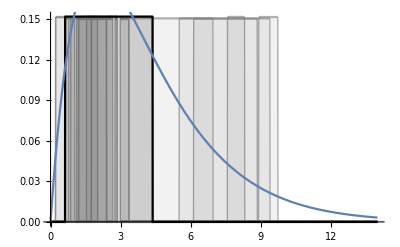

```mathematica
Show[Plot[steps,{x,0,14}, PlotStyle->{{Gray, Opacity[0.6]}}, ExclusionsStyle->{{Gray, Opacity[0.6]}}, Filling->Axis, FillingStyle->{Gray, Opacity[0.1]}],
Plot[steps[[1]],{x,0,14}, PlotStyle->{{Black, Opacity[1]}}, ExclusionsStyle->{{Black, Opacity[1]}}, Filling->Axis, FillingStyle->{Gray, Opacity[0.1]}],
Plot[PDF[GammaDistribution[2,2],x],{x,0,14}]]
```

Smooth :

```mathematica
Plot[PDF[GammaDistribution[2,2],x],{x,0,14}]
```

-Graphics-

Spike a_i(τ):

```mathematica
spikedraws = RandomVariate[GammaDistribution[2,2],20]
```

{3.02935,1.55485,6.18645,2.09694,1.76527,5.72499,5.18378,3.16469,10.1237,1.81729,1.35568,3.12613,7.3413,3.38804,2.56587,4.00169,2.20224,3.03906,1.94628,5.87427}

```mathematica
makearrows[xval_]:=Arrow[{{xval, 0},{xval, 0.15}}]
```

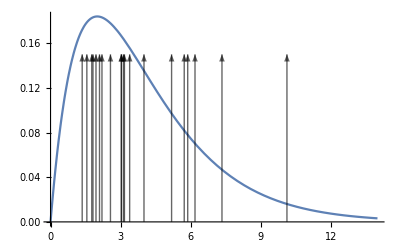

```mathematica
Show[Plot[PDF[GammaDistribution[2,2],x],{x,0,14}],
Graphics[{Black, Opacity[0.6], makearrows[#]&/@spikedraws}]]
```